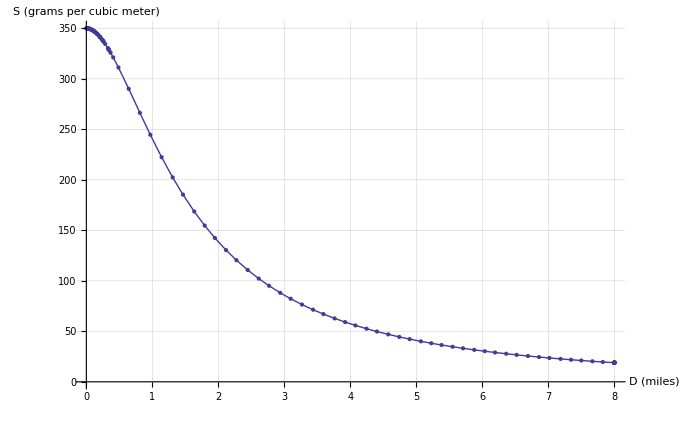

```mathematica
xMax=2*0.621;  (* Converted to miles *)
cMax=350;
B=xMax^3*2;
A=cMax*(xMax^3+B)/xMax;
xShift=xMax;

(*c[x_]=Piecewise[{{cMax,0≤x<xMax},{A*x/((x)^3+B)-1,x≥xMax}}];  *) (* Convert from g m-3 to lb per gallon *)
c[x_]=A*(x+xShift)/((x+xShift)^3+B);   (* Convert from g m-3 to lb per gallon *)
Plot[c[x],{x,0,8},AxesLabel->{Style["D (miles)",14,Bold],Style["S (grams per cubic meter)",14,Bold]},AxesOrigin->{0,0},PlotRange->{0,cMax},Mesh->All,PlotStyle->{Thick},LabelStyle->Directive[18],GridLines->Automatic,GridLinesStyle->Directive[Dashed,Black],AspectRatio->1/GoldenRatio]
```

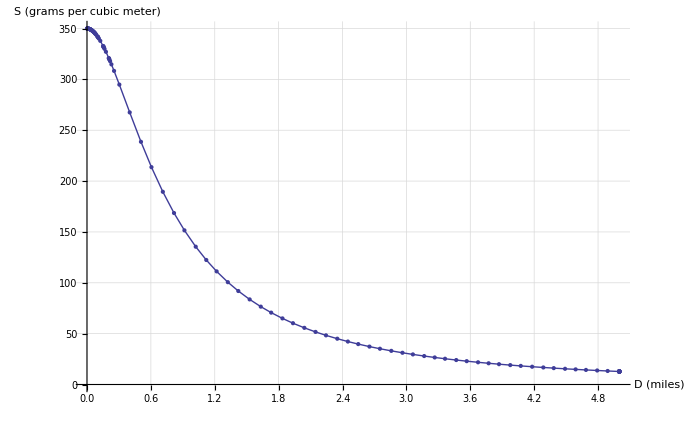

```mathematica
xMax=1*0.621;  (* Converted to miles *)
cMax=350;
B=xMax^3*2;
A=cMax*(xMax^3+B)/xMax;
xShift=xMax;

(*c[x_]=Piecewise[{{cMax,0≤x<xMax},{A*x/((x)^3+B)-1,x≥xMax}}];  *) (* Convert from g m-3 to lb per gallon *)
c[x_]=A*(x+xShift)/((x+xShift)^3+B);   (* Convert from g m-3 to lb per gallon *)
Plot[c[x],{x,0,5},AxesLabel->{Style["D (miles)",14,Bold],Style["S (grams per cubic meter)",14,Bold]},AxesOrigin->{0,0},PlotRange->{0,cMax},Mesh->All,PlotStyle->{Thick},LabelStyle->Directive[18],GridLines->Automatic,GridLinesStyle->Directive[Dashed,Black],AspectRatio->1/GoldenRatio]
```

```mathematica
vcr[t_]=75/(1+316.75*Exp[-0.699*t]);
```

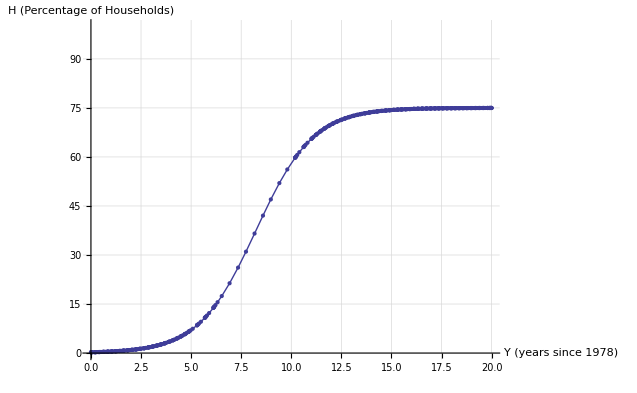

```mathematica
Plot[vcr[t],{t,0,20},AxesLabel->{Style["Y (years since 1978)",14,Bold],Style["H (Percentage of Households)",14,Bold]},AxesOrigin->{0,0},PlotRange->{0,100},Mesh->All,PlotStyle->{Thick},LabelStyle->Directive[18],GridLines->Automatic,GridLinesStyle->Directive[Dashed,Black],AspectRatio->1/GoldenRatio]
```

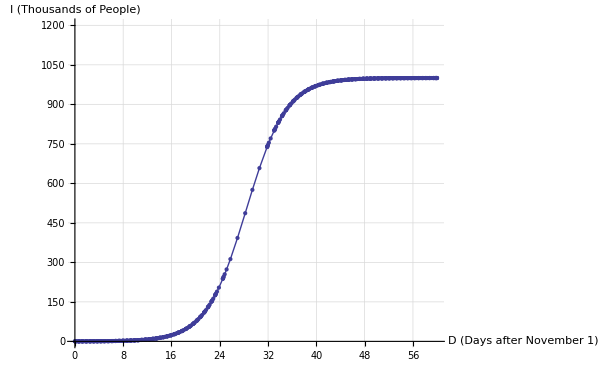

```mathematica
flu[t_]=1000/(1+5000*Exp[-0.3*t]);
Plot[flu[t],{t,0,60},AxesLabel->{Style["D (Days after November 1)",14,Bold],Style["I (Thousands of People)",14,Bold]},AxesOrigin->{0,0},PlotRange->{0,1200},Mesh->All,PlotStyle->{Thick},LabelStyle->Directive[18],GridLines->Automatic,GridLinesStyle->Directive[Dashed,Black],AspectRatio->1/GoldenRatio]
```